```mathematica
ASSIGNMENT
```

```mathematica
Q1 . Find an interval of unit length that Contains the smallest positive root of the function f(x)=x^4-3 x^2+x-10  perform 12 iterations of Bisection Method starting with resulted interval.
```

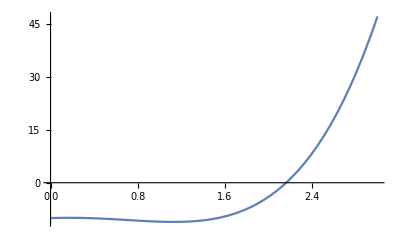

```mathematica
Bisection[a0_,b0_,n_,f_]:=
Module [{a = N[a0],b=N[b0]},
c=(a+b)/2;
i=0
If[f[a]*f[b]>0,Print["we cannot continue with the bisection method as ",f,"(a).",f,"(b)>=0"];Return[]];
output={{i,a,c,b,f[c]}};
While[i<n,If[Sign[f[b]]==Sign[f[c]],b=c,a=c;];c=(a+b)/2;i=i+1; output=Append[output, {i,a,c,b,f[c]}];];
Print[NumberForm[TableForm[output,TableHeadings->{None,{"i","a_i","c_i","b_i","f[c_i]"}}],16]];
Print["Approximate root after ",i," iterations is ",NumberForm[c,16]];
Print["Function value at approximated root,f[c]=",NumberForm[f[c],16]];]
f[x_]=x^4-3 x^2+x-10;
Plot[f[x],{x,0,3}]
```

### we can choose the interval of unit length [2, 3] as the smallest positive root around 2.5, belongs to it

```mathematica
Bisection[2, 3, 12, f];
```

i | a_i | c_i | b_i | f[c_i]
0 | 2. | 2.5 | 3. | 12.8125
1 | 2. | 2.25 | 2.5 | 2.69140625
2 | 2. | 2.125 | 2.25 | -1.031005859375
3 | 2.125 | 2.1875 | 2.25 | 0.7297515869140625
4 | 2.125 | 2.15625 | 2.1875 | -0.1749410629272461
5 | 2.15625 | 2.171875 | 2.1875 | 0.2712278962135315
6 | 2.15625 | 2.1640625 | 2.171875 | 0.0466114915907383
7 | 2.15625 | 2.16015625 | 2.1640625 | -0.06454621977172792
8 | 2.16015625 | 2.162109375 | 2.1640625 | -0.00906291579303797
9 | 2.162109375 | 2.1630859375 | 2.1640625 | 0.01875037580703065
10 | 2.162109375 | 2.16259765625 | 2.1630859375 | 0.004837755005667077
11 | 2.162109375 | 2.162353515625 | 2.16259765625 | -0.002114073766389168
12 | 2.162353515625 | 2.1624755859375 | 2.16259765625 | 0.001361467229262558

Approximate root after 12 iterations is 2.1624755859375

Function value at approximated root,f[c]=0.001361467229262558

### Q2.Perform 4 iterations of the Newton Raphson Method to obtain approximate value of (17)^(1/3) starting with the initial approximation x0=2.

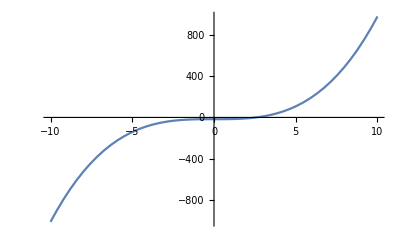

k | xk | f[xk]
0 | 2 | -9
1 | 2.75 | 3.796875
2 | 2.582644628 | 0.2263772599
3 | 2.571331512 | 0.0009901837441
4 | 2.571281592 | 1.922353121×10^-8

Root after 4 iterations xk = 2.571281592

Function value at approximated root,f[xk] = 1.922353121×10^-8

```mathematica
NewtonRaphson[x0_,n_,f_]:=Module[{xk1,xk=N[x0]},k=0; Output= {{k,x0,f[x0]}};While[k<n,fPrimexk=f'[xk]; If[fPrimexk==0,Print["The derivative of function at ",k,"th iteration is zero,we can not proceed further with the iterative scheme"];Break[]];xk1=xk-f[xk]/fPrimexk;xk=xk1;k++;Output=Append[Output,{k,xk,f[xk]}];];Print[NumberForm[TableForm[Output,TableHeadings->{None,{"k","xk","f[xk]"}}],10]];Print["Root after ",n," iterations xk = ",NumberForm[xk,10]];Print["Function value at approximated root,f[xk] = ",NumberForm[f[xk],10]];];
f[x_]= x^3-17;
Plot[f[x],{x,-10,10}]
NewtonRaphson[2,4,f]
```

#### Q3. Solve the system of equations 4 x_1 +x_2 + x_3 = 2 x_1 + 5 x_2 +2 x_3 = -6 x_1 + 2 x_2 +3 x_3= -4 with the inital vector x^(0) = (0.5,-0.5,-0.5). Perform 15 iterations.

```mathematica
GaussJacobi[A0_,B0_,X0_, max_] := 
Module[{A = N[A0], B = N[B0], i,j,k = 0, n = Length[X0], X = X0, Xk= X0},
Print[Subscript["X", 0], "=", X];
While[k < max,
For[ i = 1, i≤ n, i++,
X_[[i]] = 1/A_[[i,i]](B_[[i]] + A_[[i,i]] Xk_[[i]] - ∑_(j=1)^n A_[[i,j]] Xk_[[j]])];

Print[Subscript["X", k+1] ,"=", X];
Xk = X;
k = k+1;];
Print[" No. of iterarations performed ",max];
Return[X];];
A= {{4,1,1},{1,5,2},{1,2,3}};
B = {2,-6,-4};
X0 = {0.5,-0.5,-0.5};
GaussJacobi[A,B,X0,15]
```

X_0={0.5,-0.5,-0.5}

X_1={0.75,-1.1,-1.16667}

X_2={1.06667,-0.883333,-0.85}

X_3={0.933333,-1.07333,-1.1}

X_4={1.04333,-0.946667,-0.928889}

X_5={0.968889,-1.03711,-1.05}

X_6={1.02178,-0.973778,-0.964889}

X_7={0.984667,-1.0184,-1.02474}

X_8={1.01079,-0.987037,-0.982622}

X_9={0.992415,-1.00911,-1.01224}

X_10={1.00534,-0.993588,-0.9914}

X_11={0.996247,-1.00451,-1.00605}

X_12={1.00264,-0.996828,-0.995744}

X_13={0.998143,-1.00223,-1.00299}

X_14={1.00131,-0.998431,-0.997894}

X_15={0.999081,-1.0011,-1.00148}

No. of iterarations performed 15

{0.999081,-1.0011,-1.00148}